```mathematica
(* Can just run entire file *)
```

```mathematica
(* ds^2 = g_{\mu\nu} dx^\mu dx^\nu *)

(* ds^2 = g'_{\mu'\nu'} dx'^\mu dx'^\nu = g'_{\mu'\nu'} (dx'^\mu/dx^j) (dx'^\nu/dx^k) dx^j dx^k *)

(* So g' = Inverse(dx'/dx).g.Inverse(dx'/dx) .  That is, we want to transform g'_{\alpha\beta} = g_{\mu\nu} using dx^\nu/dx'^\alpha  dx^\mu/dx'^\beta  *)
```

```mathematica
xold={Sin[h]*Cos[ph],Sin[h]*Sin[ph],Cos[h]}
rotmat={{Cos[b0],0,-Sin[b0]},{0,1,0},{Sin[b0],0,Cos[b0]}}
xnew=rotmat.xold
```

{Cos[ph] Sin[h],Sin[h] Sin[ph],Cos[h]}

{{Cos[b0],0,-Sin[b0]},{0,1,0},{Sin[b0],0,Cos[b0]}}

{-Cos[h] Sin[b0]+Cos[b0] Cos[ph] Sin[h],Sin[h] Sin[ph],Cos[b0] Cos[h]+Cos[ph] Sin[b0] Sin[h]}

```mathematica
FullSimplify[Det[rotmat]]
```

1

```mathematica
myxnew={Sin[hnew]*Cos[phnew],Sin[hnew]*Sin[phnew],Cos[hnew]}
```

{Cos[phnew] Sin[hnew],Sin[hnew] Sin[phnew],Cos[hnew]}

```mathematica
xoldvsxnew=Inverse[rotmat].myxnew
```

{(Cos[hnew] Sin[b0])/(Cos[b0]^2+Sin[b0]^2)+(Cos[b0] Cos[phnew] Sin[hnew])/(Cos[b0]^2+Sin[b0]^2),Sin[hnew] Sin[phnew],(Cos[b0] Cos[hnew])/(Cos[b0]^2+Sin[b0]^2)-(Cos[phnew] Sin[b0] Sin[hnew])/(Cos[b0]^2+Sin[b0]^2)}

```mathematica
eqs=Table[myxnew[[ii]]==xnew[[ii]],{ii,1,3}]
```

{Cos[phnew] Sin[hnew]==-Cos[h] Sin[b0]+Cos[b0] Cos[ph] Sin[h],Sin[hnew] Sin[phnew]==Sin[h] Sin[ph],Cos[hnew]==Cos[b0] Cos[h]+Cos[ph] Sin[b0] Sin[h]}

```mathematica
eqs[[1]]
```

Cos[phnew] Sin[hnew]==-Cos[h] Sin[b0]+Cos[b0] Cos[ph] Sin[h]

```mathematica
consts={ph->0,h->0,b0->Pi/2}
```

{ph→0,h→0,b0→π/2}

```mathematica
rotmat//.consts
```

{{0,0,-1},{0,1,0},{1,0,0}}

```mathematica
xold//.consts
```

{0,0,1}

```mathematica
xnew//.consts
```

{-1,0,0}

```mathematica
xnewangles={Sin[hnew]*Cos[phnew],Sin[hnew]*Sin[phnew],Cos[hnew]}
xoldcart={xc,yc,zc}
```

{Cos[phnew] Sin[hnew],Sin[hnew] Sin[phnew],Cos[hnew]}

{xc,yc,zc}

```mathematica
xnewcart=rotmat.xoldcart
```

{xc Cos[b0]-zc Sin[b0],yc,zc Cos[b0]+xc Sin[b0]}

```mathematica
myeqs=xnewangles==xnewcart
```

{Cos[phnew] Sin[hnew],Sin[hnew] Sin[phnew],Cos[hnew]}=={xc Cos[b0]-zc Sin[b0],yc,zc Cos[b0]+xc Sin[b0]}

```mathematica
Solve[myeqs,{hnew,phnew}]
```

{}

```mathematica
mytnew=t
myrnew=r
```

t

r

```mathematica
(* Get myhnew,myphnew in terms of h,ph *)
```

```mathematica
ArcTan[xnewangles[[2]]/xnewangles[[1]]]
myphnew=ArcTan[xnewcart[[1]],xnewcart[[2]]]
```

ArcTan[Tan[phnew]]

ArcTan[xc Cos[b0]-zc Sin[b0],yc]

```mathematica
xnewcart
```

{xc Cos[b0]-zc Sin[b0],yc,zc Cos[b0]+xc Sin[b0]}

```mathematica
(*Sqrt[FullSimplify[xnewangles[[1]]^2+xnewangles[[2]]^2]]
myhnew=Sqrt[FullSimplify[xnewcart[[1]]^2+xnewcart[[2]]^2]]*)
R0=Sqrt[xnewangles[[1]]^2+xnewangles[[2]]^2]
FullSimplify[ArcTan[R0/xnewangles[[3]]]]
R=Sqrt[xnewcart[[1]]^2+xnewcart[[2]]^2]
myhnew=ArcTan[xnewcart[[3]],R]
```

√(Cos[phnew]^2 Sin[hnew]^2+Sin[hnew]^2 Sin[phnew]^2)

ArcTan[Sec[hnew] √(Sin[hnew]^2)]

√(yc^2+(xc Cos[b0]-zc Sin[b0])^2)

ArcTan[zc Cos[b0]+xc Sin[b0],√(yc^2+(xc Cos[b0]-zc Sin[b0])^2)]

```mathematica
xctest=xold[[1]]//.consts
yctest=xold[[2]]//.consts
zctest=xold[[3]]//.consts
myhnewtest=myhnew//.{xc->xctest,yc->yctest,zc->zctest,b0->Pi/2}
myphnewtest=myphnew//.{xc->xctest,yc->yctest,zc->zctest,b0->Pi/2}
xnewtest={Sin[myhnewtest]*Cos[myphnewtest],Sin[myhnewtest]*Sin[myphnewtest],Cos[myhnewtest]}
```

0

0

1

π/2

π

{-1,0,0}

```mathematica
(* Get superh,superph in terms of hnew,phnew *)
```

```mathematica
xoldangles=xold
xoldvsxnew
```

{Cos[ph] Sin[h],Sin[h] Sin[ph],Cos[h]}

{(Cos[hnew] Sin[b0])/(Cos[b0]^2+Sin[b0]^2)+(Cos[b0] Cos[phnew] Sin[hnew])/(Cos[b0]^2+Sin[b0]^2),Sin[hnew] Sin[phnew],(Cos[b0] Cos[hnew])/(Cos[b0]^2+Sin[b0]^2)-(Cos[phnew] Sin[b0] Sin[hnew])/(Cos[b0]^2+Sin[b0]^2)}

```mathematica
ArcTan[xoldangles[[2]]/xoldangles[[1]]]
superph=ArcTan[xoldvsxnew[[1]],xoldvsxnew[[2]]]
superph=FullSimplify[superph]
```

ArcTan[Tan[ph]]

ArcTan[(Cos[hnew] Sin[b0])/(Cos[b0]^2+Sin[b0]^2)+(Cos[b0] Cos[phnew] Sin[hnew])/(Cos[b0]^2+Sin[b0]^2),Sin[hnew] Sin[phnew]]

ArcTan[Cos[hnew] Sin[b0]+Cos[b0] Cos[phnew] Sin[hnew],Sin[hnew] Sin[phnew]]

```mathematica
R0old=Sqrt[xoldangles[[1]]^2+xoldangles[[2]]^2]
FullSimplify[ArcTan[R0old/xoldangles[[3]]]]
Roldvsxnew=Sqrt[xoldvsxnew[[1]]^2+xoldvsxnew[[2]]^2]
superh=ArcTan[xoldvsxnew[[3]],Roldvsxnew]
superh=FullSimplify[superh]
```

√(Cos[ph]^2 Sin[h]^2+Sin[h]^2 Sin[ph]^2)

ArcTan[Sec[h] √(Sin[h]^2)]

√(((Cos[hnew] Sin[b0])/(Cos[b0]^2+Sin[b0]^2)+(Cos[b0] Cos[phnew] Sin[hnew])/(Cos[b0]^2+Sin[b0]^2))^2+Sin[hnew]^2 Sin[phnew]^2)

ArcTan[(Cos[b0] Cos[hnew])/(Cos[b0]^2+Sin[b0]^2)-(Cos[phnew] Sin[b0] Sin[hnew])/(Cos[b0]^2+Sin[b0]^2),√(((Cos[hnew] Sin[b0])/(Cos[b0]^2+Sin[b0]^2)+(Cos[b0] Cos[phnew] Sin[hnew])/(Cos[b0]^2+Sin[b0]^2))^2+Sin[hnew]^2 Sin[phnew]^2)]

ArcTan[Cos[b0] Cos[hnew]-Cos[phnew] Sin[b0] Sin[hnew],√((Cos[hnew] Sin[b0]+Cos[b0] Cos[phnew] Sin[hnew])^2+Sin[hnew]^2 Sin[phnew]^2)]

```mathematica
Print["hold=",N[CForm[superh]]//.{Cos->cos,Sin->sin,Power->pow,ArcTan->arctanmath,Sqrt->sqrt},";"]
Print["phold=",N[CForm[superph]]//.{Cos->cos,Sin->sin,Power->pow,ArcTan->arctanmath,Sqrt->sqrt},";"]
```

hold=arctanmath(cos(b0)*cos(hnew) - 1.*cos(phnew)*sin(b0)*sin(hnew),pow(pow(cos(hnew)*sin(b0) + cos(b0)*cos(phnew)*sin(hnew),2) + pow(sin(hnew),2)*pow(sin(phnew),2),0.5));

phold=arctanmath(cos(hnew)*sin(b0) + cos(b0)*cos(phnew)*sin(hnew),sin(hnew)*sin(phnew));

```mathematica
old={t,r,h,ph}
(*oldish={t,r,Sin[h],Sin[ph]}*)
new={mytnew,myrnew,myhnew,myphnew}//.{xc->Sin[h]*Cos[ph],yc->Sin[h]*Sin[ph],zc->Cos[h]}
```

{t,r,h,ph}

{t,r,ArcTan[Cos[b0] Cos[h]+Cos[ph] Sin[b0] Sin[h],√((-Cos[h] Sin[b0]+Cos[b0] Cos[ph] Sin[h])^2+Sin[h]^2 Sin[ph]^2)],ArcTan[-Cos[h] Sin[b0]+Cos[b0] Cos[ph] Sin[h],Sin[h] Sin[ph]]}

```mathematica
(* now get old h,ph in terms of hnew,phnew *)
```

```mathematica
(*Solve[{shnew==new[[3]],sphnew==new[[4]]},{h,ph}]*)
```

```mathematica
eqs
```

{Cos[phnew] Sin[hnew]==-Cos[h] Sin[b0]+Cos[b0] Cos[ph] Sin[h],Sin[hnew] Sin[phnew]==Sin[h] Sin[ph],Cos[hnew]==Cos[b0] Cos[h]+Cos[ph] Sin[b0] Sin[h]}

```mathematica
(*
ArcTan[xnewangles[[2]]/xnewangles[[1]]]
myphnew=ArcTan[xnewcart[[1]],xnewcart[[2]]]
*)
```

```mathematica
xnew[[1]]
xnew[[2]]
xnew[[3]]
```

-Cos[h] Sin[b0]+Cos[b0] Cos[ph] Sin[h]

Sin[h] Sin[ph]

Cos[b0] Cos[h]+Cos[ph] Sin[b0] Sin[h]

```mathematica
Solve[eqs,{h,ph}][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{ph→-ArcCos[-(√(Sin[b0]^4-2 Cos[phnew]^2 Sin[b0]^2 Sin[hnew]^2+Cos[phnew]^4 Sin[hnew]^4+Cos[b0]^2 Sin[b0]^2 Sin[hnew]^2 Sin[phnew]^2-Sin[b0]^4 Sin[hnew]^2 Sin[phnew]^2+2 Cos[b0] Cos[hnew] Cos[phnew] Sin[b0] Sin[hnew]^3 Sin[phnew]^2+Cos[b0]^2 Cos[phnew]^2 Sin[hnew]^4 Sin[phnew]^2+Cos[phnew]^2 Sin[b0]^2 Sin[hnew]^4 Sin[phnew]^2-Cos[b0]^2 Sin[b0]^2 Sin[hnew]^4 Sin[phnew]^4))/(√(Sin[b0]^4-2 Cos[phnew]^2 Sin[b0]^2 Sin[hnew]^2+Cos[phnew]^4 Sin[hnew]^4+2 Cos[b0]^2 Sin[b0]^2 Sin[hnew]^2 Sin[phnew]^2+2 Cos[b0]^2 Cos[phnew]^2 Sin[hnew]^4 Sin[phnew]^2+Cos[b0]^4 Sin[hnew]^4 Sin[phnew]^4))],h→-ArcCos[(Cos[b0] Cos[hnew]-Cos[phnew] Sin[b0] Sin[hnew])/(Cos[b0]^2+Sin[b0]^2)]}

```mathematica
(*superph=-ArcCos[-(√(Sin[b0]^4-2 Cos[phnew]^2 Sin[b0]^2 Sin[hnew]^2+Cos[phnew]^4 Sin[hnew]^4+Cos[b0]^2 Sin[b0]^2 Sin[hnew]^2 Sin[phnew]^2-Sin[b0]^4 Sin[hnew]^2 Sin[phnew]^2+2 Cos[b0] Cos[hnew] Cos[phnew] Sin[b0] Sin[hnew]^3 Sin[phnew]^2+Cos[b0]^2 Cos[phnew]^2 Sin[hnew]^4 Sin[phnew]^2+Cos[phnew]^2 Sin[b0]^2 Sin[hnew]^4 Sin[phnew]^2-Cos[b0]^2 Sin[b0]^2 Sin[hnew]^4 Sin[phnew]^4))/(√(Sin[b0]^4-2 Cos[phnew]^2 Sin[b0]^2 Sin[hnew]^2+Cos[phnew]^4 Sin[hnew]^4+2 Cos[b0]^2 Sin[b0]^2 Sin[hnew]^2 Sin[phnew]^2+2 Cos[b0]^2 Cos[phnew]^2 Sin[hnew]^4 Sin[phnew]^2+Cos[b0]^4 Sin[hnew]^4 Sin[phnew]^4))]
superh=ArcCos[(Cos[b0] Cos[hnew]-Cos[phnew] Sin[b0] Sin[hnew])/(Cos[b0]^2+Sin[b0]^2)]*)
```

```mathematica
superh//.{b0->0}
FullSimplify[superph//.{b0->0},{hnew>=0,phnew≥0}]
```

ArcTan[Cos[hnew],√(Cos[phnew]^2 Sin[hnew]^2+Sin[hnew]^2 Sin[phnew]^2)]

ArcTan[Cos[phnew] Sin[hnew],Sin[hnew] Sin[phnew]]

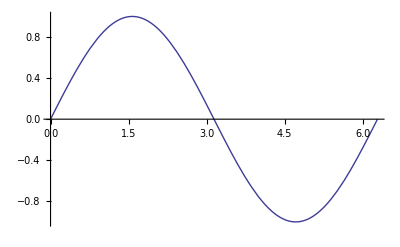

```mathematica
Plot[Sin[superph]//.{b0->0,hnew->Pi/2},{phnew,0,2*Pi}]
```

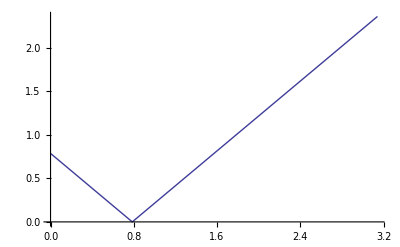

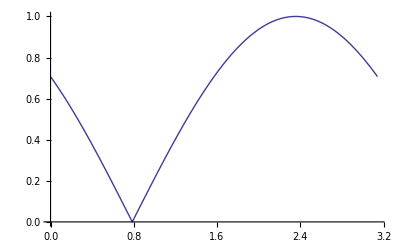

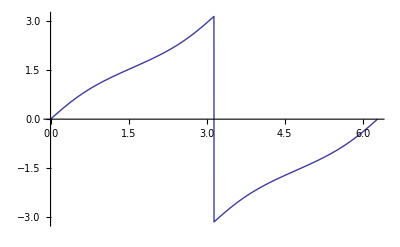

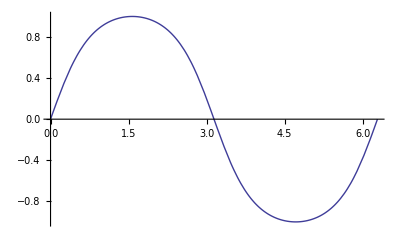

```mathematica
Plot[new[[3]]//.{b0->Pi/4,ph->0},{h,0,Pi}]
Plot[Sin[new[[3]]]//.{b0->Pi/4,ph->0},{h,0,Pi}]
Plot[new[[4]]//.{b0->Pi/4,h->Pi/2},{ph,0,2*Pi}]
Plot[Sin[new[[4]]]//.{b0->Pi/4,h->Pi/2},{ph,0,2*Pi}]
```

```mathematica
transmat=Table[D[new[[ii]],old[[jj]]],{ii,1,4},{jj,1,4}]
```

{{1,0,0,0},{0,1,0,0},{0,0,((Cos[b0] Cos[h]+Cos[ph] Sin[b0] Sin[h]) (2 (-Cos[h] Sin[b0]+Cos[b0] Cos[ph] Sin[h]) (Cos[b0] Cos[h] Cos[ph]+Sin[b0] Sin[h])+2 Cos[h] Sin[h] Sin[ph]^2))/(2 √((-Cos[h] Sin[b0]+Cos[b0] Cos[ph] Sin[h])^2+Sin[h]^2 Sin[ph]^2) ((-Cos[h] Sin[b0]+Cos[b0] Cos[ph] Sin[h])^2+(Cos[b0] Cos[h]+Cos[ph] Sin[b0] Sin[h])^2+Sin[h]^2 Sin[ph]^2))-((Cos[h] Cos[ph] Sin[b0]-Cos[b0] Sin[h]) √((-Cos[h] Sin[b0]+Cos[b0] Cos[ph] Sin[h])^2+Sin[h]^2 Sin[ph]^2))/((-Cos[h] Sin[b0]+Cos[b0] Cos[ph] Sin[h])^2+(Cos[b0] Cos[h]+Cos[ph] Sin[b0] Sin[h])^2+Sin[h]^2 Sin[ph]^2),((Cos[b0] Cos[h]+Cos[ph] Sin[b0] Sin[h]) (2 Cos[ph] Sin[h]^2 Sin[ph]-2 Cos[b0] Sin[h] (-Cos[h] Sin[b0]+Cos[b0] Cos[ph] Sin[h]) Sin[ph]))/(2 √((-Cos[h] Sin[b0]+Cos[b0] Cos[ph] Sin[h])^2+Sin[h]^2 Sin[ph]^2) ((-Cos[h] Sin[b0]+Cos[b0] Cos[ph] Sin[h])^2+(Cos[b0] Cos[h]+Cos[ph] Sin[b0] Sin[h])^2+Sin[h]^2 Sin[ph]^2))+(Sin[b0] Sin[h] Sin[ph] √((-Cos[h] Sin[b0]+Cos[b0] Cos[ph] Sin[h])^2+Sin[h]^2 Sin[ph]^2))/((-Cos[h] Sin[b0]+Cos[b0] Cos[ph] Sin[h])^2+(Cos[b0] Cos[h]+Cos[ph] Sin[b0] Sin[h])^2+Sin[h]^2 Sin[ph]^2)},{0,0,(Cos[h] (-Cos[h] Sin[b0]+Cos[b0] Cos[ph] Sin[h]) Sin[ph])/((-Cos[h] Sin[b0]+Cos[b0] Cos[ph] Sin[h])^2+Sin[h]^2 Sin[ph]^2)-(Sin[h] (Cos[b0] Cos[h] Cos[ph]+Sin[b0] Sin[h]) Sin[ph])/((-Cos[h] Sin[b0]+Cos[b0] Cos[ph] Sin[h])^2+Sin[h]^2 Sin[ph]^2),(Cos[ph] Sin[h] (-Cos[h] Sin[b0]+Cos[b0] Cos[ph] Sin[h]))/((-Cos[h] Sin[b0]+Cos[b0] Cos[ph] Sin[h])^2+Sin[h]^2 Sin[ph]^2)+(Cos[b0] Sin[h]^2 Sin[ph]^2)/((-Cos[h] Sin[b0]+Cos[b0] Cos[ph] Sin[h])^2+Sin[h]^2 Sin[ph]^2)}}

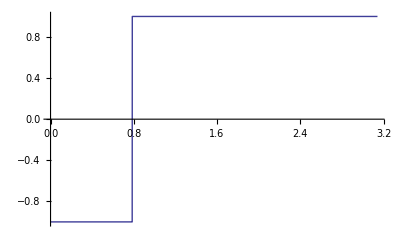

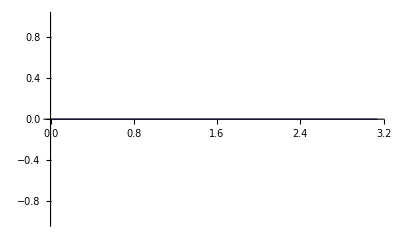

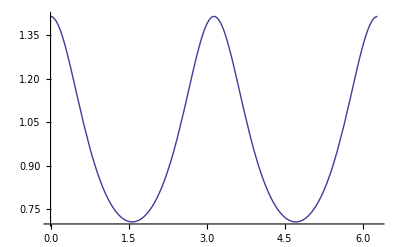

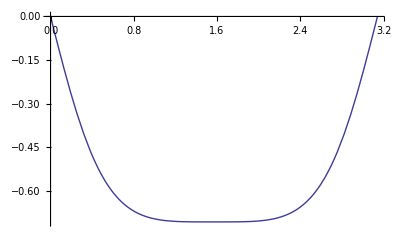

```mathematica
Plot[transmat[[3,3]]//.{r->1,b0->Pi/4,ph->0},{h,0,Pi}]
Plot[transmat[[3,4]]//.{r->1,b0->Pi/4,ph->0},{h,0,Pi}]
Plot[transmat[[4,4]]//.{r->1,b0->Pi/4,h->Pi/2},{ph,0,2*Pi}]
Plot[transmat[[4,3]]//.{r->1,b0->Pi/4,h->Pi/2},{ph,0,Pi}]
```

```mathematica
transmatfs=FullSimplify[transmat]
```

{{1,0,0,0},{0,1,0,0},{0,0,(-Cos[h] Cos[ph] Sin[b0]+Cos[b0] Sin[h])/(√((Cos[h] Sin[b0]-Cos[b0] Cos[ph] Sin[h])^2+Sin[h]^2 Sin[ph]^2)),(Sin[b0] Sin[h] Sin[ph])/(√((Cos[h] Sin[b0]-Cos[b0] Cos[ph] Sin[h])^2+Sin[h]^2 Sin[ph]^2))},{0,0,-(Sin[b0] Sin[ph])/((Cos[h] Sin[b0]-Cos[b0] Cos[ph] Sin[h])^2+Sin[h]^2 Sin[ph]^2),(Sin[h] (-Cos[h] Cos[ph] Sin[b0]+Cos[b0] Sin[h]))/((Cos[h] Sin[b0]-Cos[b0] Cos[ph] Sin[h])^2+Sin[h]^2 Sin[ph]^2)}}

```mathematica
MatrixForm[transmatfs]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | (-Cos[h] Cos[ph] Sin[b0]+Cos[b0] Sin[h])/(√((Cos[h] Sin[b0]-Cos[b0] Cos[ph] Sin[h])^2+Sin[h]^2 Sin[ph]^2)) | (Sin[b0] Sin[h] Sin[ph])/(√((Cos[h] Sin[b0]-Cos[b0] Cos[ph] Sin[h])^2+Sin[h]^2 Sin[ph]^2))
0 | 0 | -(Sin[b0] Sin[ph])/((Cos[h] Sin[b0]-Cos[b0] Cos[ph] Sin[h])^2+Sin[h]^2 Sin[ph]^2) | (Sin[h] (-Cos[h] Cos[ph] Sin[b0]+Cos[b0] Sin[h]))/((Cos[h] Sin[b0]-Cos[b0] Cos[ph] Sin[h])^2+Sin[h]^2 Sin[ph]^2))

```mathematica
Table[Print["trans[",ii-1,"][",jj-1,"]=",N[CForm[transmatfs[[ii,jj]]]//.{Cos->cos,Sin->sin,Power->pow}],";"],{ii,1,4},{jj,1,4}]
```

trans[0][0]=1.;

trans[0][1]=0.;

trans[0][2]=0.;

trans[0][3]=0.;

trans[1][0]=0.;

trans[1][1]=1.;

trans[1][2]=0.;

trans[1][3]=0.;

trans[2][0]=0.;

trans[2][1]=0.;

trans[2][2]=pow(pow(cos(h)*sin(b0) - 1.*cos(b0)*cos(ph)*sin(h),2.) + pow(sin(h),2.)*pow(sin(ph),2.),-0.5)*(-1.*cos(h)*cos(ph)*sin(b0) + cos(b0)*sin(h));

trans[2][3]=pow(pow(cos(h)*sin(b0) - 1.*cos(b0)*cos(ph)*sin(h),2.) + pow(sin(h),2.)*pow(sin(ph),2.),-0.5)*sin(b0)*sin(h)*sin(ph);

trans[3][0]=0.;

trans[3][1]=0.;

trans[3][2]=-1.*pow(pow(cos(h)*sin(b0) - 1.*cos(b0)*cos(ph)*sin(h),2.) + pow(sin(h),2.)*pow(sin(ph),2.),-1.)*sin(b0)*sin(ph);

trans[3][3]=pow(pow(cos(h)*sin(b0) - 1.*cos(b0)*cos(ph)*sin(h),2.) + pow(sin(h),2.)*pow(sin(ph),2.),-1.)*sin(h)*(-1.*cos(h)*cos(ph)*sin(b0) + cos(b0)*sin(h));

{{Null,Null,Null,Null},{Null,Null,Null,Null},{Null,Null,Null,Null},{Null,Null,Null,Null}}

```mathematica
FullSimplify[transmatfs//.{b0->0}]
```

{{1,0,0,0},{0,1,0,0},{0,0,Csc[h] √(Sin[h]^2),0},{0,0,0,1}}

```mathematica
itrans=Inverse[transmatfs];
itrans=FullSimplify[itrans]
```

{{1,0,0,0},{0,1,0,0},{0,0,((-Cos[h] Cos[ph] Sin[b0]+Cos[b0] Sin[h]) √((Cos[h] Sin[b0]-Cos[b0] Cos[ph] Sin[h])^2+Sin[h]^2 Sin[ph]^2))/((Cos[h] Cos[ph] Sin[b0]-Cos[b0] Sin[h])^2+Sin[b0]^2 Sin[ph]^2),-Sin[b0] Sin[ph]},{0,0,(Csc[h] Sin[b0] Sin[ph] √((Cos[h] Sin[b0]-Cos[b0] Cos[ph] Sin[h])^2+Sin[h]^2 Sin[ph]^2))/((Cos[h] Cos[ph] Sin[b0]-Cos[b0] Sin[h])^2+Sin[b0]^2 Sin[ph]^2),Cos[b0]-Cos[ph] Cot[h] Sin[b0]}}

```mathematica
Table[Print["trans[",ii-1,"][",jj-1,"]=",N[CForm[itrans[[ii,jj]]]//.{Cos->cos,Sin->sin,Power->pow,Cot->cot,Csc->csc}],";"],{ii,1,4},{jj,1,4}]
```

trans[0][0]=1.;

trans[0][1]=0.;

trans[0][2]=0.;

trans[0][3]=0.;

trans[1][0]=0.;

trans[1][1]=1.;

trans[1][2]=0.;

trans[1][3]=0.;

trans[2][0]=0.;

trans[2][1]=0.;

trans[2][2]=pow(pow(cos(h)*cos(ph)*sin(b0) - 1.*cos(b0)*sin(h),2.) + pow(sin(b0),2.)*pow(sin(ph),2.),-1.)*pow(pow(cos(h)*sin(b0) - 1.*cos(b0)*cos(ph)*sin(h),2.) + pow(sin(h),2.)*pow(sin(ph),2.),0.5)*(-1.*cos(h)*cos(ph)*sin(b0) + cos(b0)*sin(h));

trans[2][3]=-1.*sin(b0)*sin(ph);

trans[3][0]=0.;

trans[3][1]=0.;

trans[3][2]=csc(h)*pow(pow(cos(h)*cos(ph)*sin(b0) - 1.*cos(b0)*sin(h),2.) + pow(sin(b0),2.)*pow(sin(ph),2.),-1.)*pow(pow(cos(h)*sin(b0) - 1.*cos(b0)*cos(ph)*sin(h),2.) + pow(sin(h),2.)*pow(sin(ph),2.),0.5)*sin(b0)*sin(ph);

trans[3][3]=cos(b0) - 1.*cos(ph)*cot(h)*sin(b0);

{{Null,Null,Null,Null},{Null,Null,Null,Null},{Null,Null,Null,Null},{Null,Null,Null,Null}}

```mathematica
g={{-1,0,0,0},{0,1,0,0},{0,0,r^2,0},{0,0,0,r^2*Sin[h]^2}}
```

{{-1,0,0,0},{0,1,0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[h]^2}}

```mathematica
gnew=FullSimplify[Table[Sum[itrans[[ii,jj]]*g[[jj,kk]]*itrans[[pp,kk]],{jj,1,4},{kk,1,4}],{ii,1,4},{pp,1,4}]]
```

$Aborted

```mathematica
FullSimplify[gnew//.{b0->Pi/2},{h≥0,h≤Pi}]
```

{{-1,0,0,0},{0,1,0,0},{0,0,r^2 (Sin[h]^2 Sin[ph]^2+(Cos[h]^2 Cos[ph]^2 (Cos[h]^2+Sin[h]^2 Sin[ph]^2))/((Cos[h]^2 Cos[ph]^2+Sin[ph]^2)^2)),r^2 Cos[h] Cos[ph] Sin[ph] (Sin[h]-(Cos[h] Cot[h]+Sin[h] Sin[ph]^2)/((Cos[h]^2 Cos[ph]^2+Sin[ph]^2)^2))},{0,0,r^2 Cos[h] Cos[ph] Sin[ph] (Sin[h]-(Cos[h] Cot[h]+Sin[h] Sin[ph]^2)/((Cos[h]^2 Cos[ph]^2+Sin[ph]^2)^2)),r^2 (Cos[h]^2 Cos[ph]^2+(Sin[ph]^2 (Cot[h]^2+Sin[ph]^2))/((Cos[h]^2 Cos[ph]^2+Sin[ph]^2)^2))}}

```mathematica
(* Expensive *)
(*FullSimplify[gnew//.{h->superh,ph->superph},{hnew≥0,phnew≥0,b0≥0}]*)
```

```mathematica
T1=itrans[[3,3]];
T2=itrans[[4,3]];
P1=itrans[[3,4]];
P2=itrans[[4,4]];
g33fragile=r^2*T1^2+r^2*Sin[h]^2*P1^2;
g34fragile=(r^2*T1*T2+r^2*Sin[h]^2*P1*P2);
g43fragile=g34fragile;
g44fragile=r^2*T2^2+r^2*Sin[h]^2*P2^2;
```

```mathematica
(*FullSimplify[gnew[[4,4]]-g44fragile]*)
```

```mathematica
FullSimplify[itrans.transmat]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
dettrans=FullSimplify[Det[transmat]]
detitrans=FullSimplify[Det[itrans]]
detsq=FullSimplify[Det[g]]
detnewsq=FullSimplify[Det[gnew]]
```

Sin[h]/(√((Cos[h] Sin[b0]-Cos[b0] Cos[ph] Sin[h])^2+Sin[h]^2 Sin[ph]^2))

Csc[h] √((Cos[h] Sin[b0]-Cos[b0] Cos[ph] Sin[h])^2+Sin[h]^2 Sin[ph]^2)

-r^4 Sin[h]^2

1/16 r^4 (-10+2 Cos[2 b0]+3 Cos[2 (b0-h)]+2 Cos[2 h]+3 Cos[2 (b0+h)]+8 Cos[2 ph] Sin[b0]^2 Sin[h]^2+8 Cos[ph] Sin[2 b0] Sin[2 h])

```mathematica
detsq//.{b0->0,r->1,ph->0}
detnewsq//.{b0->0,r->1,ph->0}
detnewsq//.{b0->Pi/4,r->1,ph->0,h->Pi/4}
detnewsq//.{b0->Pi/4,r->1,ph->0,h->Pi/2}
```

-Sin[h]^2

1/16 (-8+8 Cos[2 h])

0

-1/2

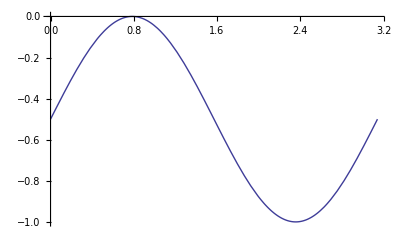

```mathematica
Plot[detnewsq//.{r->1,b0->Pi/4,ph->0},{h,0,Pi}]
```

```mathematica
old
new
```

{t,r,h,ph}

{t,r,ArcTan[Cos[b0] Cos[h]+Cos[ph] Sin[b0] Sin[h],√((-Cos[h] Sin[b0]+Cos[b0] Cos[ph] Sin[h])^2+Sin[h]^2 Sin[ph]^2)],ArcTan[-Cos[h] Sin[b0]+Cos[b0] Cos[ph] Sin[h],Sin[h] Sin[ph]]}

```mathematica
sinsqnewh=Sin[myhnew]^2//.{xc->Sin[h]*Cos[ph],yc->Sin[h]*Sin[ph],zc->Cos[h]}
```

Sin[ArcTan[Cos[b0] Cos[h]+Cos[ph] Sin[b0] Sin[h],√((-Cos[h] Sin[b0]+Cos[b0] Cos[ph] Sin[h])^2+Sin[h]^2 Sin[ph]^2)]]^2

```mathematica
N[(gnew[[3,3]]/r^2)//.{b0->Pi/4,h->Pi/3,ph->Pi/7}]
N[(g33fragile/r^2)//.{b0->Pi/4,h->Pi/3,ph->Pi/7}]
```

0.549011

0.549011

```mathematica
N[sinsqnewh//.{b0->Pi/4,h->Pi/3,ph->Pi/7}]
N[(gnew[[4,4]]/r^2)//.{b0->Pi/4,h->Pi/3,ph->Pi/7}]
N[(g44fragile/r^2)//.{b0->Pi/4,h->Pi/3,ph->Pi/7}]
```

0.180465

0.781783

0.781783

```mathematica
N[(gnew[[3,4]]/r^2)//.{b0->Pi/4,h->Pi/3,ph->Pi/7}]
N[(g34fragile/r^2)//.{b0->Pi/4,h->Pi/3,ph->Pi/7}]
```

0.498741

0.498741

```mathematica
N[(gnew[[4,3]]/r^2)//.{b0->Pi/4,h->Pi/3,ph->Pi/7}]
N[(g43fragile/r^2)//.{b0->Pi/4,h->Pi/3,ph->Pi/7}]
```

0.498741

0.498741

(0.141191 (0.188255+(0.450484-0.866025 Cot[h])^2))/((0.141191+(0.780262 Cos[h]-0.5 Sin[h])^2)^2)+(0.780262 Cos[h]-0.5 Sin[h])^2

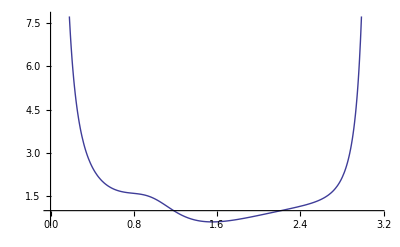

(r^2 (0.5-0.780262 Cot[h])^2 Sin[h]^2+(0.141191 r^2 Csc[h]^2 ((0.866025 Cos[h]-0.450484 Sin[h])^2+0.188255 Sin[h]^2))/((0.141191+(0.780262 Cos[h]-0.5 Sin[h])^2)^2))/r^2

-Graphics-

```mathematica
it=N[(gnew[[4,4]]/r^2)//.{b0->Pi/3.0,ph->Pi/7}]
Plot[it,{h,0,Pi}]
itf=N[(g44fragile/r^2)//.{b0->Pi/3.0,ph->Pi/7}]
Plot[itf,{h,0,Pi}]
```

0.375754 ((0.780262 Cos[h]-0.5 Sin[h]) Sin[h]+(Csc[h] (-0.780262 Cos[h]+0.5 Sin[h]) ((0.866025 Cos[h]-0.450484 Sin[h])^2+0.188255 Sin[h]^2))/((0.141191+(0.780262 Cos[h]-0.5 Sin[h])^2)^2))

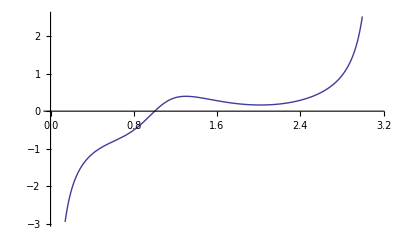

(-0.375754 r^2 (0.5-0.780262 Cot[h]) Sin[h]^2+(0.375754 r^2 Csc[h] (-0.780262 Cos[h]+0.5 Sin[h]) ((0.866025 Cos[h]-0.450484 Sin[h])^2+0.188255 Sin[h]^2))/((0.141191+(0.780262 Cos[h]-0.5 Sin[h])^2)^2))/r^2

-Graphics-

```mathematica
it=N[(gnew[[3,4]]/r^2)//.{b0->Pi/3.0,ph->Pi/7}]
Plot[it,{h,0,Pi}]
itf=N[(g34fragile/r^2)//.{b0->Pi/3.0,ph->Pi/7}]
Plot[itf,{h,0,Pi}]
```

0.141191 Sin[h]^2+((0.780262 Cos[h]-0.5 Sin[h])^2 ((0.866025 Cos[h]-0.450484 Sin[h])^2+0.188255 Sin[h]^2))/((0.141191+(0.780262 Cos[h]-0.5 Sin[h])^2)^2)

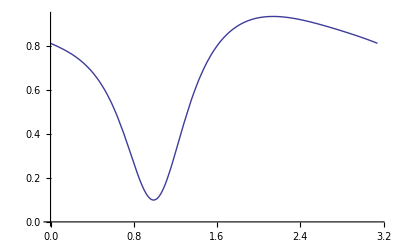

(0.141191 r^2 Sin[h]^2+(r^2 (-0.780262 Cos[h]+0.5 Sin[h])^2 ((0.866025 Cos[h]-0.450484 Sin[h])^2+0.188255 Sin[h]^2))/((0.141191+(0.780262 Cos[h]-0.5 Sin[h])^2)^2))/r^2

-Graphics-

```mathematica
it=N[(gnew[[3,3]]/r^2)//.{b0->Pi/3.0,ph->Pi/7}]
Plot[it,{h,0,Pi}]
itf=N[(g33fragile/r^2)//.{b0->Pi/3.0,ph->Pi/7}]
Plot[itf,{h,0,Pi}]
```

```mathematica
N[sinsqnewh//.{b0->Pi/4,h->Pi/2+Pi/4,ph->0}]
```

1.

```mathematica
g[[4,4]]
```

r^2 Sin[h]^2

```mathematica
(*sols=Solve[xnewangles==xnew,{hnew,phnew}]*)
```

```mathematica
(*FullSimplify[sols]//.{(-1+Cos[b0] Cos[h]+Cos[ph] Sin[b0] Sin[h]) (1+Cos[b0] Cos[h]+Cos[ph] Sin[b0] Sin[h])->bottom,-(Cos[h] Sin[b0]-Cos[b0] Cos[ph] Sin[h])^2->top}*)
```

```mathematica
(* test coordinate rotation *)
consts1={b0->Pi/4.0,hnew->Pi/7,phnew->Pi/17}
N[consts1]
testh=superh//.consts1
testph=superph//.consts1

consts2={b0->Pi/4.0,h->testh,ph->testph}

xoldtest=xold//.consts2(*xc,yc,zc*)
xnewtest=xnew//.consts2 (*xcnew,ycnew,zcnew*)
myhnew//.{b0->Pi/4.0,xc->xoldtest[[1]],yc->xoldtest[[2]],zc->xoldtest[[3]]}
myphnew//.{b0->Pi/4.0,xc->xoldtest[[1]],yc->xoldtest[[2]],zc->xoldtest[[3]]}

(* correct rotation, since final new values of hnew,phnew agree with original input values *)
```

{b0→0.785398,hnew→π/7,phnew→π/17}

{b0→0.785398,hnew→0.448799,phnew→0.1848}

1.22866

0.0847326

{b0→0.785398,h→1.22866,ph→0.0847326}

{0.938659,0.0797259,0.335503}

{0.426496,0.0797259,0.900969}

0.448799

0.1848

```mathematica
(* Vertical field rotate *)
```

```mathematica
Acov={0,0,0,r^rpow*Sin[h]^hpow}
Acovnew=Table[Sum[itrans[[ii,jj]]*Acov[[jj]],{jj,1,4}],{ii,1,4}]
```

{0,0,0,r^rpow Sin[h]^hpow}

{0,0,-r^rpow Sin[b0] Sin[h]^hpow Sin[ph],r^rpow (Cos[b0]-Cos[ph] Cot[h] Sin[b0]) Sin[h]^hpow}

```mathematica
Acovnew[[1]]
Acovnew[[2]]
```

0

0

```mathematica
CForm[Acovnew[[3]]]//.{Power->pow,Cos->cos,Cot->cot,Sin->sin,b0->FIELDROT,h->th}
```

-(pow(r,rpow)*pow(sin(th),hpow)*sin(FIELDROT)*sin(ph))

```mathematica
CForm[Acovnew[[4]]]//.{Power->pow,Cos->cos,Cot->cot,Sin->sin,b0->FIELDROT,h->th}
```

pow(r,rpow)*pow(sin(th),hpow)*
   (cos(FIELDROT) - cos(ph)*cot(th)*sin(FIELDROT))